```mathematica
create[f_] := 1/Sqrt[2 hbar m w] (-hbar D[f, x] + m w x f)
```

```mathematica
phi0:= (m w/(Pi hbar))^(1/4) Exp[-m w/(2 hbar) x^2]
```

```mathematica
hbar = m = w = 1
```

1

```mathematica
phin[n_]:= 1/Sqrt[n!] Nest[create,phi0,n]
```

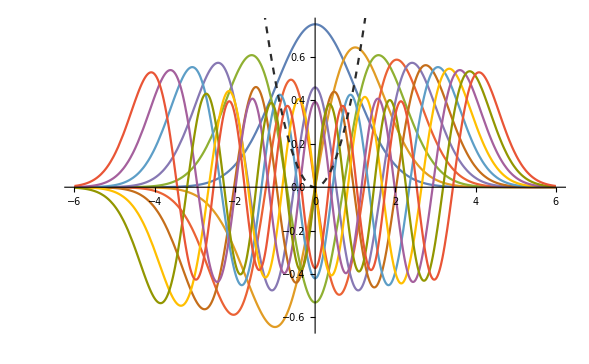

```mathematica
Show[Plot[Evaluate[Table[phin[n],{n,0,10,1}]],{x,-6,6},PlotRange->Full],Plot[1/2 m w^2 x^2,{x,-5,5} ,PlotStyle->Dashed,ColorFunction->GrayLevel]]
```

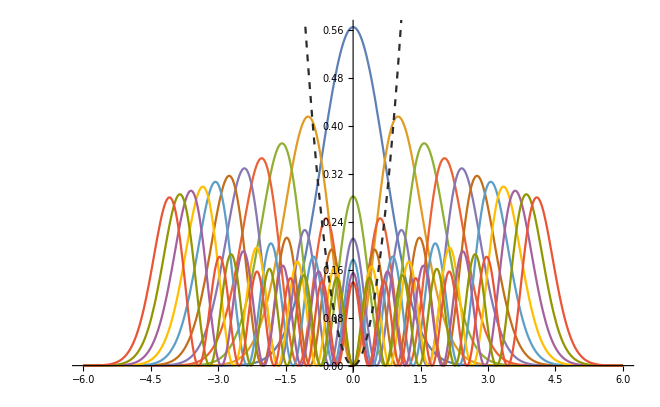

```mathematica
Show[Plot[Evaluate[Table[phin[n]^2,{n,0,10,1}]],{x,-6,6},PlotRange->Full],Plot[1/2 m w^2 x^2,{x,-5,5} ,PlotStyle->Dashed,ColorFunction->GrayLevel]]
```

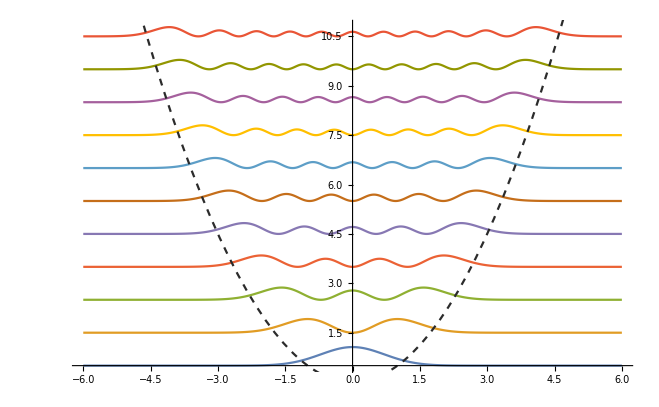

```mathematica
Show[Plot[Evaluate[Table[phin[n]^2 + (n+1/2)hbar w,{n,0,10,1}]],{x,-6,6},PlotRange->Full],Plot[1/2 m w^2 x^2,{x,-5,5} ,PlotStyle->Dashed,ColorFunction->GrayLevel]]
```

```mathematica
limit[n_]:=Solve[1/2 m w^2 x^2 == (n+1/2)hbar w,x]
limitSet:=Table[limit[n],{n,0,10,1}]
```

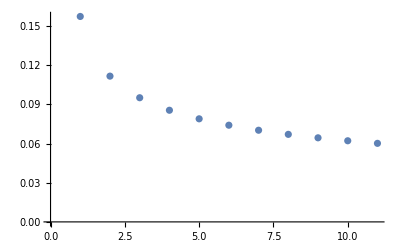

```mathematica
ListPlot[Table[N[1 - Integrate[phin[n]^2,{x,-Sqrt[1 + 2 n],Sqrt[1 + 2 n]}]],{n,0,10,1}]]
```

```mathematica
Part[limitSet,4]
```

{{x→-√7},{x→√7}}

```mathematica
limitSet
```

{{{x→-1},{x→1}},{{x→-√3},{x→√3}},{{x→-√5},{x→√5}},{{x→-√7},{x→√7}},{{x→-3},{x→3}},{{x→-√11},{x→√11}},{{x→-√13},{x→√13}},{{x→-√15},{x→√15}},{{x→-√17},{x→√17}},{{x→-√19},{x→√19}},{{x→-√21},{x→√21}}}

```mathematica
Table[N[1 - Integrate[phin[n]^2,{x,-Sqrt[1 + 2 n],Sqrt[1 + 2 n]}]],{n,0,10,1}]
```

{0.157299,0.11161,0.0950694,0.0854829,0.0789264,0.0740342,0.0701809,0.0670313,0.0643863,0.0621191,0.0601438}